```mathematica
ClearAll["Global`*"];
```

# Reacción enzimática

Considera una reacción enzimática donde la concentración de la enzima  no es constante, sino que decae como ,  y  constantes positivas. Supón que la concentración inicial de sustrato es .
Resuelve la ecuación diferencial  donde  y  son constantes positivas. Muestra que  tiende a una constante positiva en el limite .

Hagamos primero una observación acerca de  simplemente de la ecuación diferencial. Dado que   y  son siempre positivas entonces la derivada de  es negativa para toda , por lo tanto la función  debe ser decreciente. Ahora si, resolvamos la ecuación. 

Procederemos por separación de variables, es decir, dejando de un lado la variable dependiente  y del otro la variable independiente .

Integrando ambos lados nos queda:

```mathematica
Subscript[I, 1] = Integrate[((Subscript[K, m]+S[t])/S[t]),S[t]]
```

S[t]+Log[S[t]] K_m

```mathematica
Subscript[I, 2] = Integrate[- k E0 e^(-c t),t]
```

(e^(-c t) E0 k)/(c Log[e])

Así nuestra solución queda de forma implícita como: 

  
 
 donde  representa las constantes de integración de  e . Considerando  podemos encontrar el valor de

Por lo tanto nuestra solución dada la condición inicial  es:

Ahora, si queremos ver el comportamiento de  cuando  tomemos limite de ambos lados:

como  es continua tenemos la siguiente igualdad:

.

Si suponemos que  entonces como  tendríamos
 	lo cual no es posible pues . Por lo tanto  
 
  Podemos concluir que  debe ser una constante positiva pues como ya observamos  es decreciente y su limite no es cero.

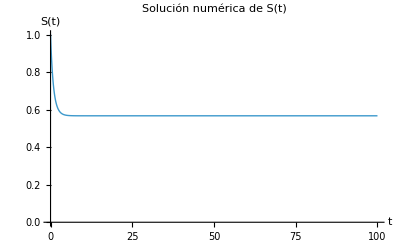

```mathematica
(* Definir parámetros numéricos *)
k = 1;
Km = 1;
c = 1;
(* Resolver la ecuación diferencial numéricamente *)
sol = NDSolve[
   {S'[t] == - (k*Exp[-c*t]*S[t])/(Km + S[t]), S[0] == 1},
   S,
   {t, 0, 100}
];

(* Graficar la solución S(t) *)
Plot[
  Evaluate[S[t] /. sol],
  {t, 0, 100},
  PlotLabel -> "Solución numérica de S(t)",
  AxesLabel -> {"t", "S(t)"},
  PlotRange -> {Automatic, {0, 1}},
  PlotStyle -> Thick
]
```